```mathematica
(*1. 定义四种斯格明子自旋方向函数)
Switch[kind,1,{fx,fy}={-y,x}/r,2,{fx,fy}={y,-x}/r,3,{fx,fy}={x,y}/r,4,{fx,fy}={-x,-y}/r];
{fx,fy}*Exp[-r/1.5]]
```

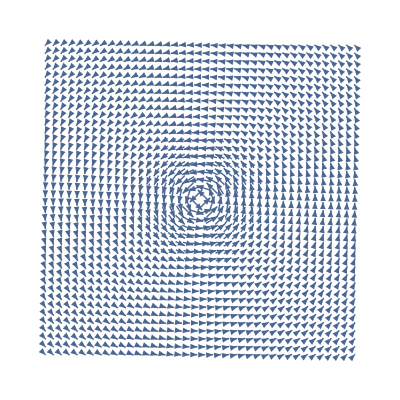

```mathematica
(*2. 形态1：奈尔型斯格明子 Néel Skyrmion（图e）*)(* ==============================================*)VectorPlot[spin[x,y,1],{x,-3,3},{y,-3,3},VectorPoints->40,VectorScale->Tiny,Frame->False,Axes->False]
```

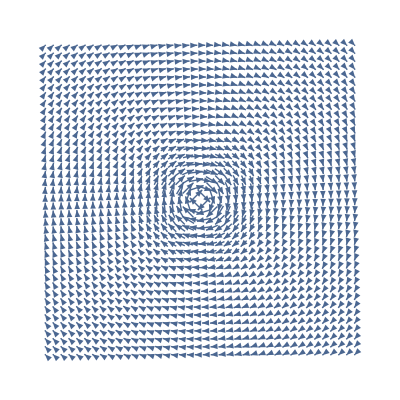

```mathematica
(*3. 形态2：反斯格明子 Anti-Skyrmion（图a）*)(* ==============================================*)VectorPlot[spin[x,y,2],{x,-3,3},{y,-3,3},VectorPoints->40,VectorScale->Tiny,Frame->False,Axes->False]
```

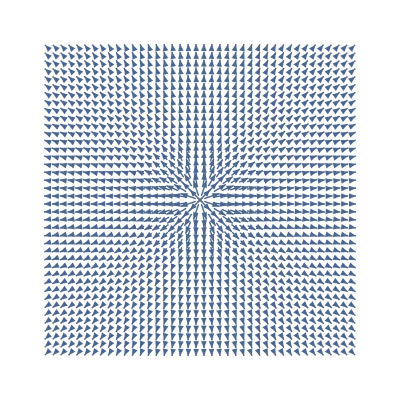

```mathematica
(*4. 形态3：双半子 Bimeron 1（图i）*)(* ==============================================*)VectorPlot[spin[x,y,3],{x,-3,3},{y,-3,3},VectorPoints->40,VectorScale->Tiny,Frame->False,Axes->False]
```

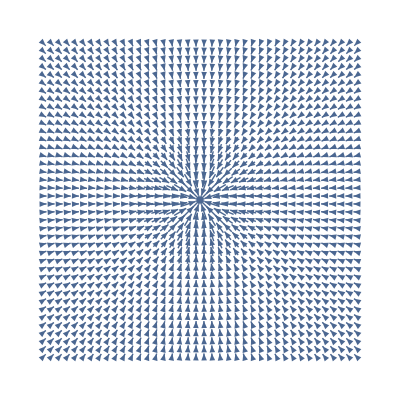

```mathematica
(*5. 形态4：双半子 Bimeron 2（图m）*)
(* ==============================================*)
VectorPlot[spin[x,y,4],{x,-3,3},{y,-3,3},VectorPoints->40,VectorScale->Tiny,Frame->False,Axes->False]
```